## P3.3

```mathematica
nt=2.42;
ni=1;
```

```mathematica
thetat=ArcSin[ni*Sin[thetai Degree]/nt];
```

```mathematica
rs=(ni*Cos[thetai Degree]-nt*Cos[thetat Degree])/(ni*Cos[thetai Degree]+nt*Cos[thetat Degree]);
ts=(2*ni*Cos[thetai Degree])/(ni*Cos[thetai Degree]+nt*Cos[thetat Degree]);
rp=(ni*Cos[thetat Degree]-nt*Cos[thetai Degree])/(ni*Cos[thetat Degree]+nt*Cos[thetai Degree]);
tp=(2*ni*Cos[thetai Degree])/(ni*Cos[thetat Degree]+nt*Cos[thetai Degree]);
```

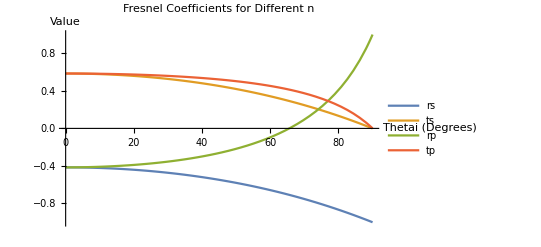

```mathematica
Plot[{rs,ts,rp,tp},{thetai,0,90},PlotLabel->"Fresnel Coefficients for Different n",PlotLegends->{"rs","ts","rp","tp"},AxesLabel->{"Thetai (Degrees)","Value"}]
```

```mathematica
FindRoot[rp,{thetai,65}]
```

{thetai→65.5931}

```mathematica
(*Brewster's Angle is 65.5931 Degrees*)
```

## L3.4

```mathematica
nt3=1.54;
ni3=1;
```

```mathematica
thetat=ArcSin[ni3*Sin[thetai Degree]/nt3];
```

```mathematica
(*Calculate the Fresnel Coefficients for L3*)
```

```mathematica
rs3=(ni3*Cos[thetai Degree]-nt3*Cos[thetat Degree])/(ni3*Cos[thetai Degree]+nt3*Cos[thetat Degree]);
ts3=(2*ni3*Cos[thetai Degree])/(ni3*Cos[thetai Degree]+nt3*Cos[thetat Degree]);
rp3=(ni3*Cos[thetat Degree]-nt3*Cos[thetai Degree])/(ni3*Cos[thetat Degree]+nt3*Cos[thetai Degree]);
tp3=(2*ni3*Cos[thetai Degree])/(ni3*Cos[thetat Degree]+nt3*Cos[thetai Degree]);
```

```mathematica
(*Insert the data from the experiment*)
```

```mathematica
s={{5,.065},{10,.073},{20,.082},{30,.120},{40,.174},{50,.240},{57,.300},{60,.370},{70,.640},{80,1.03}};
p={{5,.115},{10,.113},{20,.097},{30,.071},{40,.043},{50,.027},{57,.023},{60,.035},{70,.141},{80,.57}};
```

```mathematica
(*Plot the calcuated Fresnel Coefficients*)
```

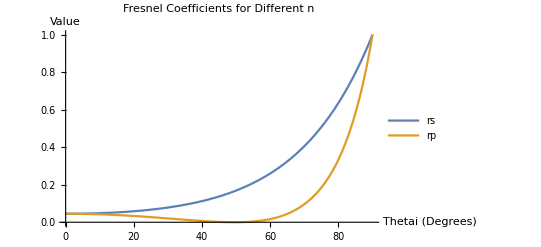

```mathematica
Plot[{rs3^2,rp3^2},{thetai,0,90},PlotLabel->"Fresnel Coefficients for Different n",PlotLegends->{"rs","rp"},AxesLabel->{"Thetai (Degrees)","Value"}]
```

```mathematica
(*Plot the experimental data as a ListLinePlot*)
```

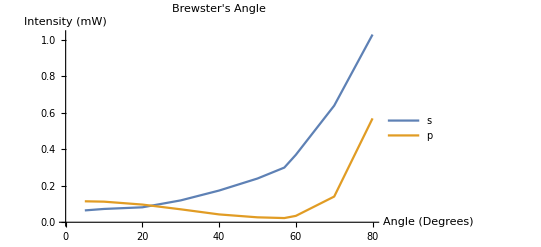

```mathematica
ListLinePlot[{s,p},PlotLegends->{"s","p"},PlotLabel->"Brewster's Angle",AxesLabel->{"Angle (Degrees)","Intensity (mW)"}]
```

```mathematica
(*Now put them on the same graph*)
```

```mathematica
data={s,p};
```

```mathematica
lines = Fit[s, {1,x,x^2},x]
linep = Fit[p, {1,x,x^2},x]
```

0.171585-0.0121241 x+0.000274332 x^2

0.261662-0.0160204 x+0.000227211 x^2

```mathematica
(*I put lines of best fit for good measure*)
```

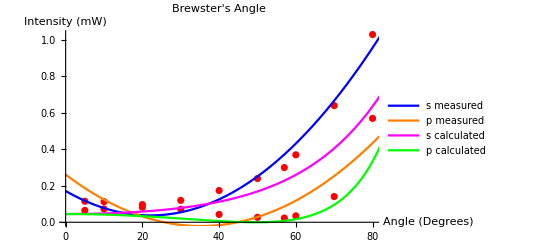

```mathematica
Show[ListPlot[data, PlotStyle->Red], Plot[{lines, linep}, {x, 0, 90},PlotStyle->{Blue,Orange},PlotLegends->{"s measured","p measured"}],Plot[{rs3^2,rp3^2},{thetai,0,90},PlotStyle->{Magenta,Green},PlotLegends->{"s calculated","p calculated"}],PlotLabel->"Brewster's Angle",AxesLabel->{"Angle (Degrees)","Intensity (mW)"}]
```

## P3.7

```mathematica
ni7=1;
nt7=1.5;
```

```mathematica
thetaB=ArcTan[nt7/ni7 ]
```

0.982794

```mathematica
(*To get it in degrees*)
```

```mathematica
thetaBd=thetaB*180/Pi
```

56.3099

```mathematica
theta7=ArcSin[Sin[thetaB]/nt7]
```

0.588003

```mathematica
theta7d=theta7*180/Pi
```

33.6901

```mathematica
Rp=(ni7*Cos[theta7 ]-nt7*Cos[thetaB ])/(ni7*Cos[theta7 ]+nt7*Cos[thetaB ])
```

0.

```mathematica
Rs=(ni7*Cos[thetaBd  Degree]-nt7*Cos[theta7d Degree])/(ni7*Cos[thetaBd  Degree]+nt7*Cos[theta7d Degree])
```

-0.384615

```mathematica
Rs^2
```

0.147929

## Problem 3.11

```mathematica
nt3=1.33;
ni3=1;
thetat=ArcSin[ni3*Sin[thetai Degree]/nt3];
```

```mathematica
rs3=(ni3*Cos[thetai Degree]-nt3*Cos[thetat Degree])/(ni3*Cos[thetai Degree]+nt3*Cos[thetat Degree]);
ts3=(2*ni3*Cos[thetai Degree])/(ni3*Cos[thetai Degree]+nt3*Cos[thetat Degree]);
rp3=(ni3*Cos[thetat Degree]-nt3*Cos[thetai Degree])/(ni3*Cos[thetat Degree]+nt3*Cos[thetai Degree]);
tp3=(2*ni3*Cos[thetai Degree])/(ni3*Cos[thetat Degree]+nt3*Cos[thetai Degree]);
```

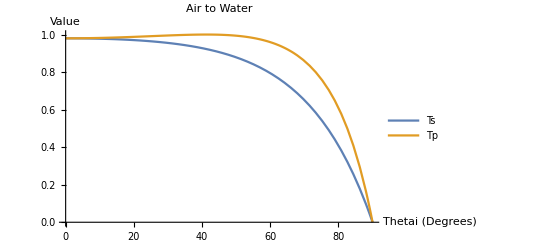

```mathematica
Plot[{1-rs3^2,1-rp3^2},{thetai,0,90},PlotLabel->"Air to Water",PlotLegends->{"Ts","Tp"},AxesLabel->{"Thetai (Degrees)","Value"}]
```

```mathematica
nt3=1;
ni3=1.33;
```

```mathematica
thetat=ArcSin[ni3*Sin[thetai Degree]/nt3];
```

```mathematica
rs3=(ni3*Cos[thetai Degree]-nt3*Cos[thetat Degree])/(ni3*Cos[thetai Degree]+nt3*Cos[thetat Degree]);
ts3=(2*ni3*Cos[thetai Degree])/(ni3*Cos[thetai Degree]+nt3*Cos[thetat Degree]);
rp3=(ni3*Cos[thetat Degree]-nt3*Cos[thetai Degree])/(ni3*Cos[thetat Degree]+nt3*Cos[thetai Degree]);
tp3=(2*ni3*Cos[thetai Degree])/(ni3*Cos[thetat Degree]+nt3*Cos[thetai Degree]);
```

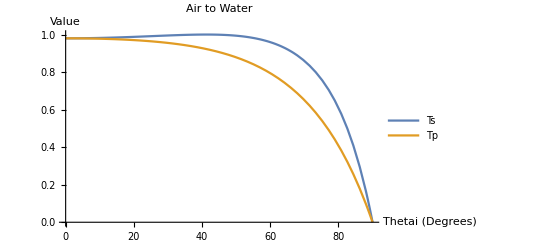

```mathematica
Plot[{1-rs3^2,1-rp3^2},{thetai,0,90},PlotLabel->"Air to Water",PlotLegends->{"Ts","Tp"},AxesLabel->{"Thetai (Degrees)","Value"}]
```